# \[MathematicaIcon]Mathematica Functies en grafieken

In de module "Logics and problem solving" is Mathematica-gebruik een hulpmiddel bij complexere berekeningen of visualisaties..  Hieronder volgen een aantal tips en afspraken om functies en grafieken op een correcte manier te implementeren.

## 1. Functies

Mathematica kent enorm veel functies, maar het komt natuurlijk ook wel eens voor dat je zelf een nieuwe functie wilt definiëren. Dat doe je als volgt:

```mathematica
f[x_]:=x^2-3x+5
```

Let hierbij op het volgende:

Je definieert een functie door een dubbele punt voor het =- teken te zetten.

De variabele (hier: x) zet je tussen enkele rechte haken, en je voegt er een _ (underscore) aan toe.

De rechterkant is een uitdrukking in deze variabele (maar zonder underscore). Je ziet weer dat Mathematica de variabele herkent, en er een andere kleur aan geeft. Deze nieuwe kleur (groen in de meeste versies) geeft aan dat de variabele alleen lokaal (dus hier: binnen de definitie van de functie) gebruikt wordt. Daarbuiten mag je x nog steeds als gewone variabele gebruiken.

De definitie van een functie heeft geen uitvoer; het maakt dus niet uit of je achter de definitie een puntkomma zet of niet.

Nadat je de functie gedefinieerd hebt, kun je die op precies dezelfde manier gebruiken als de ingebouwde Mathematica-functies.

```mathematica
f[6]
```

23

De variabele x in de functiedefinitie is een zogenaamde plaatshouder - dat wil zeggen dat Mathematica de variabele vervangt door datgene wat de gebruiker invoert als hij de functie aanroept. Dat kan dus ook een nog niet gebruikte variabele zijn:

```mathematica
f[z]
```

5-3 z+z^2

Je ziet overigens dat Mathematica de volgorde van de termen omdraait; het programma gebruikt bepaalde regels om de termen in een uitkomst te ordenen, wat af en toe leidt tot dit soort ongebruikelijke volgordes. 
Doordat de variabele x als plaatshouder fungeert, kun je ook functies in functies invullen:

```mathematica
f[Log[x]]
```

5-3 Log[x]+Log[x]^2

## 2. Grafieken

Met behulp van de functie Plot kunnen we Mathematica een grafiek van een functie laten maken:

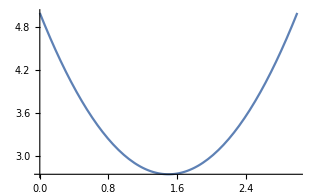

```mathematica
Plot[x^2-3x+5, {x,0,3}]
```

Het resultaat zie je in de afbeelding hierboven.

De eerste invoer in Plot (hier: x^2-3x+5) is de functie waarvan we een grafiek willen tekenen.

De tweede invoer in Plot (hier: {x, 0, 3}) is een lijst met de variabele waarvoor je de grafiek wilt tekenen, de begin- en eindwaarde.

Het zal je misschien opvallen dat Mathematica zelf de nodige keuzes maakt in het tekenen van de grafiek: de plaats van de assen (de x-as wordt hier bijvoorbeeld niet zoals gebruikelijk getekend op de hoogte y=0, maar op de hoogte y=2.5), het bereik van de y-as, de kleur van de grafiek, enz. Meestal is Mathematica slim genoeg om dergelijke keuzes goed te maken, maar vind je de uitvoer niet mooi, dan kun je vrijwel alles met behulp van opties aanpassen. Bijvoorbeeld:

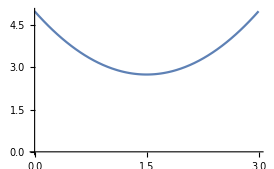

```mathematica
Plot[x^2-3x+5, {x,0,3}, AxesOrigin->{0,0}]
```

geeft de grafiek weer met de assen op de gebruikelijke plaats. Gebruik weer de helpfunctie om te zien welke opties er allemaal zijn. 
Mathematica kan ook meerdere grafieken in één afbeelding tonen. Hiervoor vervang je simpelweg de functie uit het vorige voorbeeld door een lijst (tussen accolades) van functies. Let op: alle functies moeten daarbij dezelfde variabele gebruiken! Bijvoorbeeld:

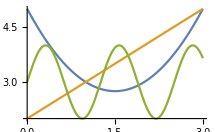

```mathematica
Plot[{x^2-3x+5, x+2, Sin[5x]+3}, {x,0,3}]
```

Het resultaat zie je in de bovenstaande afbeelding. Je ziet dat Mathematica elke grafiek een andere kleur geeft, zodat ze goed te onderscheiden zijn. Mathematica vertelt alleen niet welke grafiek bij welke functie hoort; om dat te bepalen moet je dus even nadenken, of eerst de grafieken afzonderlijk tekenen.

## 3. Met een schone lei beginnen

Een veelvoorkomende bron van fouten in het gebruik van Mathematica is dat men functies en variabelen gebruikt die al eerder een definitie of waarde gekregen hebben. Daarom is het verstandig om steeds met een schone lei te beginnen aan een volgend probleem in Mathematica. Met de volgende opdracht worden de toegewezen waarden en definities van alle symbolen met alleen maar kleine letters ongedaan gemaakt.

```mathematica
Remove["Global`*"]
```

Helpt dit niet, dan kun je nog altijd de Mathematica kernel verlaten door “Quit Kernel” (Local) te kiezen in het Evaluation menu of het commando Quit in te toetsen.

## 4. Grafieken van impliciet gedefinieerde functies

Mathematica kan meer dan grafieken van één of twee veranderlijken tekenen.
Met ContourPlot kun je grafieken van impliciet gedefinieerd functies (zoals een cirkelvergelijking) tekenen. Maar zie wat er gebeurt als je de commando’s zo maar aanroept:

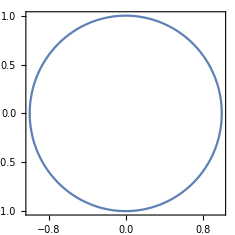

```mathematica
ContourPlot[x^2+y^2==1, {x,-1,1},{y,-1,1}, AspectRatio->Automatic]
```

## 5. Functieonderzoek

Als we de grafiek tekenen van de functie met voorschrift x^3-x^2-4x+4, zien we dat deze functie drie nulpunten heeft. Dit zijn oplossingen van de vergelijking x^3-x^2-4x+4=0. 
In Mathematica geven we dit in als volgt:

```mathematica
x^3-x^2-4x+4==0
```

4-4 x-x^2+x^3==0

Binnen een wiskundige vergelijking gebruik je in de software twee gelijkheidstekens ==. Het enkele gelijkheidsteken kun je gebruiken om een object een naam te geven. Laten we een variabele “vergelijking” maken waarin deze vergelijking opgeslagen wordt.

```mathematica
vergelijking = %
```

4-4 x-x^2+x^3==0

En nu laten we Mathematica deze vergelijking oplossen met het commando Solve:

```mathematica
oplossing = Solve[vergelijking, x]
```

{{x→-2},{x→1},{x→2}}

Hierbij gebruiken we de eerder ingetoetste naam vergelijking en we geven een nieuwe naam oplossing aan het resultaat van de Solve-opdracht. Solve heeft drie oplossingen x=-2, x=1 en x=2 gevonden voor de vergelijking en geeft de oplossingen weer als substitutieregels 
x→-2, x→1 en x→2. Door deze substitutieregels toe te passen op de uitdrukking x via de operator /., dan krijg je een lijstje van de oplossingswaarden:

```mathematica
x/. oplossing
```

{-2,1,2}

Laten we nu de eerste oplossing kiezen om mee verder te werken en deze oplossing de naamd x1 geven.

```mathematica
x1 = x/. oplossing[[1]]
```

-2

Je kunt nu verdere berekeningen gaan doen met x1, bijvoorbeeld het kwadraat ervan uitrekenen. Of je kunt deze oplossingen ook controleren door ze te substitueren in de vergelijking.

```mathematica
vergelijking /. x->x1
```

True

Het zal je wellicht niet ontgaan zijn dat er ook een functie Roots voorhanden is, deze functie geeft de wortels van een veeltermvergelijking weer. Het maakt onderliggend gebruik van de commando’s Factor en Decompose. Transcendente vergelijkingen kun je hier niet mee oplossen.

```mathematica
Roots[a x^2+b x+c==0,x]
```

x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)